### Exploring Discoverers

```mathematica
(*See GoL-10-Data* for retrieval code*) 
goodData = ;
```

```mathematica
Select[goodData, KeyExistsQ[#, "Discovered by"]&]
```

```mathematica
namesdiscoverers = Select[goodData, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

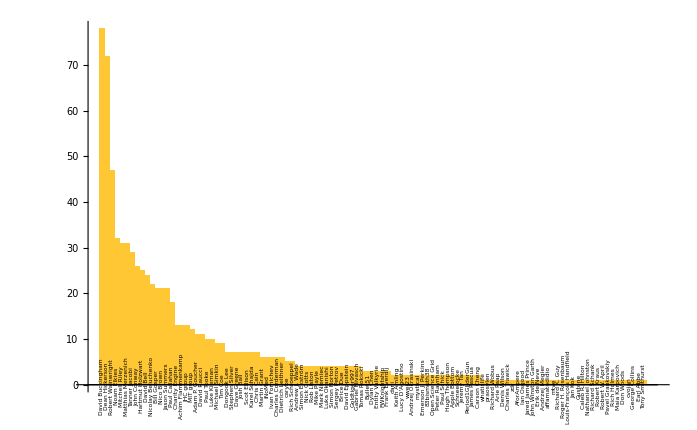

```mathematica
BarChart[ReverseSort[Counts[namesdiscoverers]],ChartLabels->Placed[Keys[ReverseSort[Counts[namesdiscoverers]]],Axis,Style[Rotate[#,Pi/2], 6]&]]
```

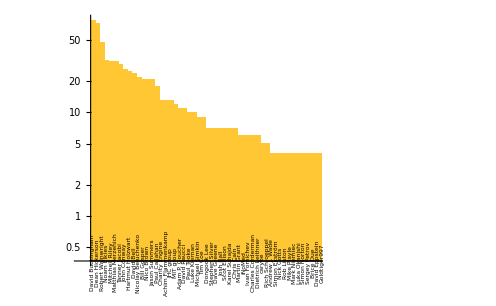

```mathematica
BarChart[ReverseSort[Counts[namesdiscoverers]],ChartLabels->Placed[Keys[ReverseSort[Counts[namesdiscoverers]]],Axis,Style[Rotate[#,Pi/2], 6]&],ScalingFunctions->"Log",PlotRange->{{-2,50},Automatic}]
```

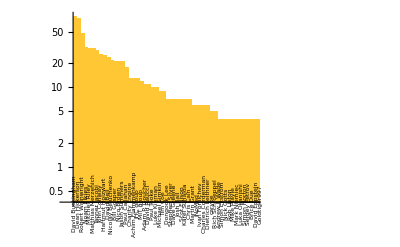

```mathematica
Rotate[%,-90Degree]
```

```mathematica
ListLogLogPlot[ReverseSort[Counts[namesdiscoverers]]]
```

-Graphics-

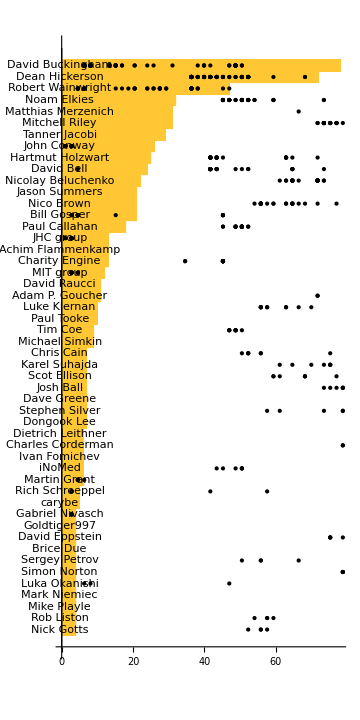

```mathematica
BarChart[Take[Sort[Counts[namesdiscoverers]],-50],ChartLabels->Placed[Keys[Take[Sort[Counts[namesdiscoverers]],-50]],Axis,(*Style[Rotate[#,Pi/2],6]*)#&],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None,Epilog->Point[{Rescale[ToExpression[#1],{1969,2025},{1,100}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[goodData,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]]
```

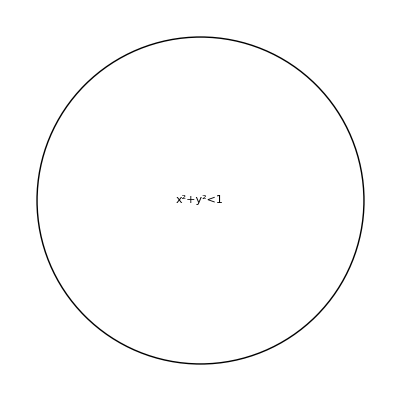

```mathematica
Graphics[{Circle[],Text[x^2+y^2<1,{0,0}]}]
```

```mathematica
Column[Text[#(*, {0, 0}*)]&/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]]]
```

Nick Gotts
Rob Liston
Mike Playle
Mark Niemiec
Luka Okanishi
Simon Norton
Sergey Petrov
Brice Due
David Eppstein
Goldtiger997
Gabriel Nivasch
carybe
Rich Schroeppel
Martin Grant
iNoMed
Ivan Fomichev
Charles Corderman
Dietrich Leithner
Dongook Lee
Stephen Silver
Dave Greene
Josh Ball
Scot Ellison
Karel Suhajda
Chris Cain
Michael Simkin
Tim Coe
Paul Tooke
Luke Kiernan
Adam P. Goucher
David Raucci
MIT group
Charity Engine
Achim Flammenkamp
JHC group
Paul Callahan
Bill Gosper
Nico Brown
Jason Summers
Nicolay Beluchenko
David Bell
Hartmut Holzwart
John Conway
Tanner Jacobi
Mitchell Riley
Matthias Merzenich
Noam Elkies
Robert Wainwright
Dean Hickerson
David Buckingham

```mathematica
Epilog->Point[{Rescale[ToExpression[#1],{1969,2025},{1,100}],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[goodData,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[{#1,First[#2]/. _Missing->-Infinity}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&]]
```

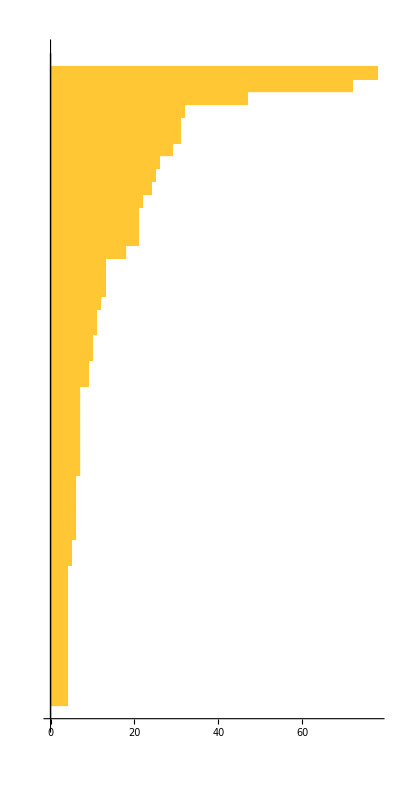

```mathematica
BarChart[Take[Sort[Counts[namesdiscoverers]],-50],BarOrigin->Left,PlotRange->100,AspectRatio->2,PlotRangePadding->None]
```

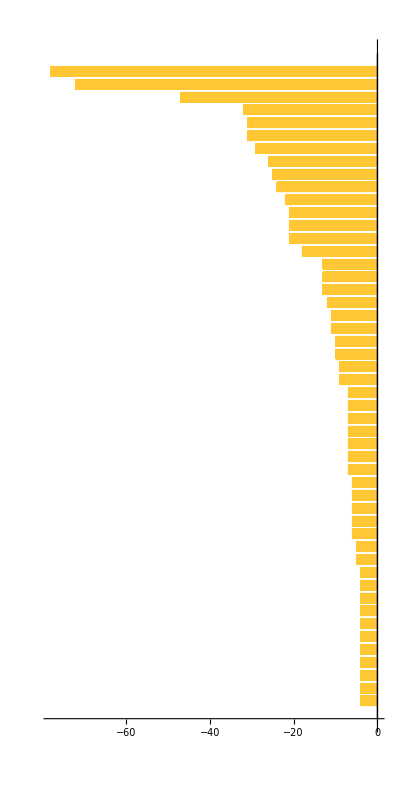
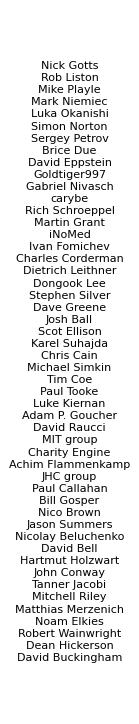

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50],BarOrigin->Right,PlotRange->100,AspectRatio->2,PlotRangePadding->None, ImageSize->{Automatic, 750}], GraphicsColumn[Text[#(*, {1, 0}*)]&/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]], Spacings->.05]}]
```